r ∈ [0., 4.];
x ∈ [0., 1.];

2.92132

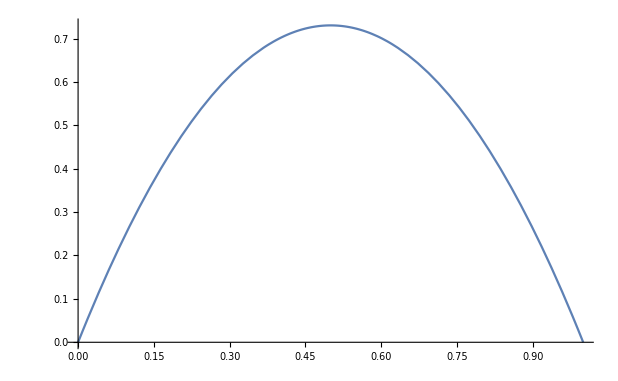

```mathematica
r=RandomReal[4.]
Plot[{r*x(1-x)},{x,0,1}]
```

r1 ∈ [0., 1.];
r2 ∈ [1., 2.];
r3 ∈ [2., 3.];
r4 ∈ [3.5, 4.];

0.511735

1.86264

2.87477

3.92323

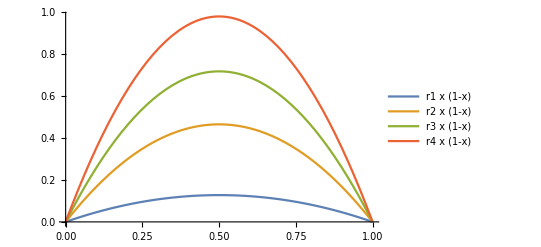

```mathematica
r1=RandomReal[{0.,1.}]
r2=RandomReal[{1.,2.}]
r3=RandomReal[{2.,3.}]
r4=RandomReal[{3.5,4.}]
Plot[{r1*x(1-x),r2*x(1-x),r3*x(1-x),r4*x(1-x)},{x,0,1},PlotLegends->"Expressions"]
```

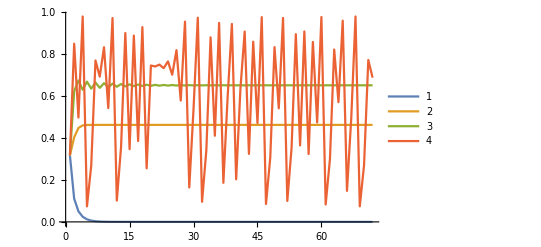

```mathematica
x0=RandomReal[]
n1=x0;n2=x0;n3=x0;n4=x0;
arr1={n1};
arr2={n2};
arr3={n3};
arr4={n4};
n=70;
For[i=0,i≤n,i++,
incr1=r1*n1(1-n1);
incr2=r2*n2(1-n2);
incr3=r3*n3(1-n3); 
incr4=r4*n4(1-n4);
n1=incr1;n2=incr2;n3=incr3;n4=incr4;
AppendTo[arr1,n1]; AppendTo[arr2,n2]; AppendTo[arr3,n3]; AppendTo[arr4,n4]]
ListLinePlot[{arr1,arr2,arr3,arr4},PlotLegends->Automatic]
```

```mathematica
n4=x0; arr4={};
For[i=0,i≤n,i++,
incr4=r4*n4(1-n4);
AppendTo[arr4,{n4,incr4}];
AppendTo[arr4,{incr4,incr4}];
n4=incr4]
```

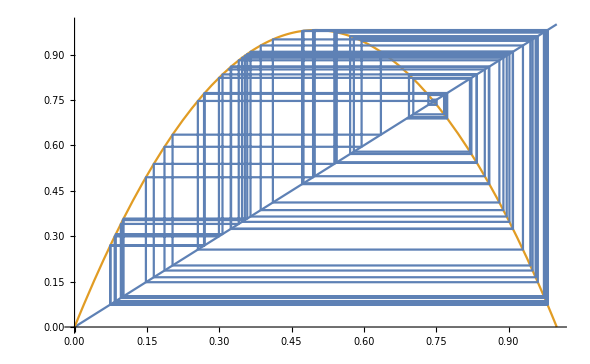

```mathematica
Show[Plot[{x,r4*x(1-x)},{x,0,1}],ListPlot[arr4,Joined->True]]
```

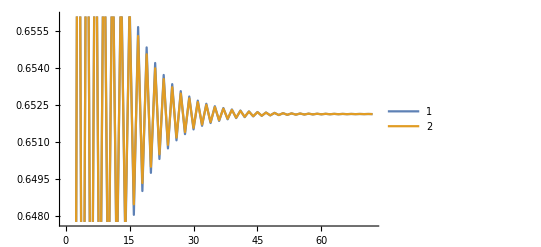

```mathematica
nincr=x0+0.01*x0;
nX=x0;
arr={nX};
arrincr={nincr};
For[i=0,i≤n,i++,
incr=r3*nX(1-nX); 
incrincr=r3*nincr(1-nincr);
nX=incr;
nincr=incrincr;
AppendTo[arr,nX]; 
AppendTo[arrincr,nincr]]
ListLinePlot[{arr,arrincr},PlotLegends->Automatic]
```